## Importacion de datos experimentales

```mathematica
SetDirectory["C:\Users\ameat\OneDrive\Música\Documentos\Calculos Mie\Respuesta de los materiales"]
```

C:\Users\ameat\OneDrive\Música\Documentos\Calculos Mie\Respuesta de los materiales

```mathematica
(**Importar datos de Au, Al, Ag, Si y SiC**)
AuTxt= Import["Au_J&C.txt","Table"]; (**refractive index**)
AgTxt= Import["1-Ag_Johnson&Christy.txt","Table"]; (**refractive index**)
SiTxt= Import["Si_Palik.txt","Table"]; (**dielectric function**)
SiCTxt= Import["SiC-6H_Palik_Jose.dat","Table"];(**refractive index**)
```

```mathematica
(**Número de puntos que se tienen**)
NDatAu=AuTxt[[1]][[1]]; (**Número de datos de Au**)
NDatAg=AgTxt[[1]][[1]]; (**Número de datos de Al**)
NDatSi=SiTxt[[1]][[1]];(**Número de datos de Si**)
NDatSiC=SiCTxt[[1]][[1]]; (**Número de datos de SiC**)
(**Selección de los puntos sin las indicaciones del documento txt**)
AuData=AuTxt[[3;;2+NDatAu]]; (**Conjunto de datos de Au**)
AgData=AgTxt[[3;;2+NDatAg]]; (**Conjunto de datos de Au**)
SiData=SiTxt[[3;;2+NDatSi]]; (**Conjunto de datos de Au**)
SiCData=SiCTxt[[3;;2+NDatSiC]]; (**Conjunto de datos de Au**)
```

```mathematica
(**Parte real e imaginaria del índice de refracción Au**)
nAuData=Table[{AuData[[i]][[1]],AuData[[i]][[2]]},{i,1,NDatAu}];
kAuData=Table[{AuData[[i]][[1]],AuData[[i]][[3]]},{i,1,NDatAu}];
(**Parte real e imaginaria del índice de refracción Ag**)
nAgData=Table[{AgData[[i]][[1]],AgData[[i]][[2]]},{i,1,NDatAg}];
kAgData=Table[{AgData[[i]][[1]],AgData[[i]][[3]]},{i,1,NDatAg}];
(**Parte real e imaginaria del índice de refracción Si**)
ϵreSiData=Table[{SiData[[i]][[1]],SiData[[i]][[2]]},{i,1,NDatSi}];
ϵimSiData=Table[{SiData[[i]][[1]],SiData[[i]][[3]]},{i,1,NDatSi}];
(**Parte real e imaginaria del índice de refracción Si**)
nSiData=Table[{SiData[[i]][[1]],Re[Sqrt[SiData[[i]][[2]]+I*SiData[[i]][[3]]]]},{i,1,NDatSi}];
kSiData=Table[{SiData[[i]][[1]],Im[Sqrt[SiData[[i]][[2]]+I*SiData[[i]][[3]]]]},{i,1,NDatSi}];
(**Parte real e imaginaria del índice de refracción Si**)
nSiCData=Table[{SiCData[[i]][[1]],SiCData[[i]][[2]]},{i,1,NDatSiC}];
kSiCData=Table[{SiCData[[i]][[1]],SiCData[[i]][[3]]},{i,1,NDatSiC}];
```

#### Interpolacion

```mathematica
nAu=Interpolation[nAuData,Method->"Spline"];
kAu=Interpolation[kAuData,Method->"Spline"];
nAg=Interpolation[nAgData,Method->"Spline"];
kAg=Interpolation[kAgData,Method->"Spline"];
nSi =Interpolation[nSiData,Method->"Spline"];
kSi=Interpolation[kSiData,Method->"Spline"];
nSiC =Interpolation[nSiCData,Method->"Spline"];
kSiC=Interpolation[kSiCData,Method->"Spline"];
```

#### Indice de refraccion

```mathematica
rfindxAu[hw_]:=nAu[hw]+I*kAu[hw]
rfindxAg[hw_]:=nAg[hw]+I*kAg[hw]
rfindxSi[hw_]:=nSi[hw]+I*kSi[hw]
rfindxSiC[hw_]:=nSiC[hw]+I*kSiC[hw]
```

#### Graficas n

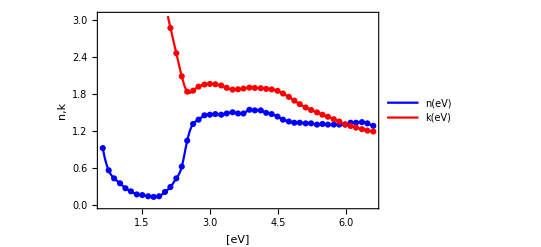

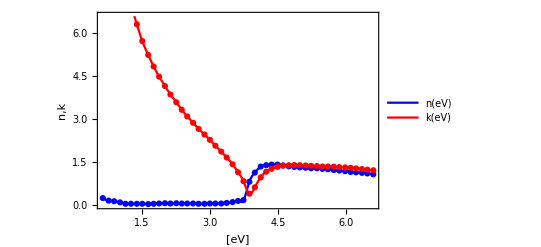

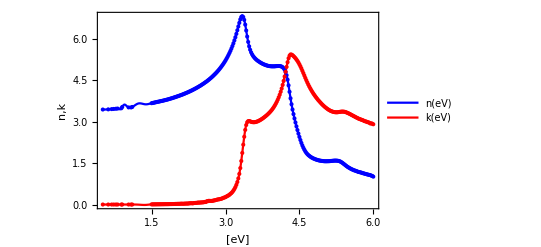

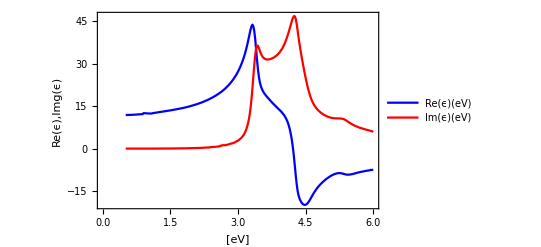

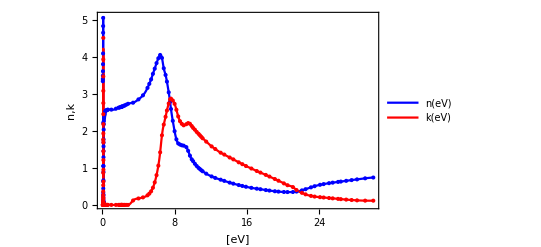

```mathematica
(**Au**)
Show[Plot[{nAu[x],kAu[x]},{x,nAuData[[1]][[1]],nAuData[[-1]][[1]]},PlotStyle->{Blue, Red},Frame->True,FrameLabel->{"[eV]","n,k","Índice de refracción de Au"},FrameStyle->Directive[Black,15, Bold],PlotLegends->Placed[{"n(eV)","k(eV)"},{Right,Top}]],ListPlot[{nAuData,kAuData},PlotStyle->{Blue,Red}]]
(***Ag***)
Show[Plot[{nAg[x],kAg[x]},{x,nAgData[[1]][[1]],nAgData[[-1]][[1]]},PlotStyle->{Blue, Red},Frame->True,FrameLabel->{"[eV]","n,k","Índice de refracción de Ag"},FrameStyle->Directive[Black,15, Bold],PlotLegends->Placed[{"n(eV)","k(eV)"},{Right,Top}]],ListPlot[{nAgData,kAgData},PlotStyle->{Blue,Red}]]

(**Si**)Show[Plot[{nSi[x],kSi[x]},{x,nSiData[[1]][[1]],nSiData[[-1]][[1]]},PlotStyle->{Blue, Red},Frame->True,FrameLabel->{"[eV]","n,k","Índice de refracción de Si"},FrameStyle->Directive[Black,15, Bold],PlotLegends->Placed[{"n(eV)","k(eV)"},{Right,Top}]],ListPlot[{nSiData,kSiData},PlotStyle->{Blue,Red}]]
ListLinePlot[{ϵreSiData,ϵimSiData},PlotStyle->{Blue,Red},PlotStyle->{Blue, Red},Frame->True,FrameLabel->{"[eV]","Re(ϵ),Img(ϵ)","Función dieléctrica de Si"},FrameStyle->Directive[Black,15, Bold],PlotLegends->Placed[{"Re(ϵ)(eV)","Im(ϵ)(eV)"},{Left,Top}]]
(***SiC***)
Show[Plot[{nSiC[x],kSiC[x]},{x,nSiCData[[1]][[1]],nSiCData[[-1]][[1]]},PlotStyle->{Blue, Red},Frame->True,FrameLabel->{"[eV]","n,k","Índice de refracción de SiC"},FrameStyle->Directive[Black,15, Bold],PlotLegends->Placed[{"n(eV)","k(eV)"},{Right,Top}]],ListPlot[{nSiCData,kSiCData},PlotStyle->{Blue,Red}]]
```

## Drude model

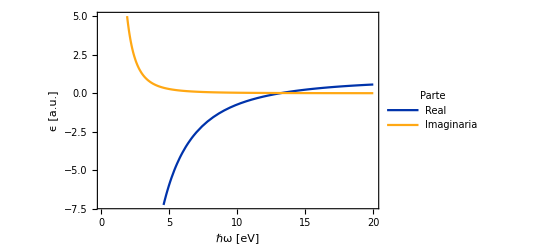

```mathematica
ϵDS[w_,wp_,γ_]:= 1 - wp^2/((w)*(w+ⅈ*γ)); (**permititividad en función de la frecuencia**) 
nDS[w_,wp_,gamma_]:=Sqrt[ϵDS[w,wp,gamma]]; (**índice de refracción con modelo de Drude en función de la frecuencia**) 
nDS1[0,w_]:=√ϵDS[w,13.144,0.19716];
NAlDeV[w_]:=Re[nDS1[0,w]];
KAlDeV[w_]:=Im[nDS1[0,w]];
(***Ag***)
Plot[{Re[ϵDS[w,13.144,0.19716]],Im[ϵDS[w,13.144,0.19716]]},{w,0.1,20},Frame->True, PlotStyle->{RGBColor[0.,0.2,0.67],RGBColor[1.,0.66,0.08]},FrameLabel->{{"ϵ [a.u.]",None},{"ℏω [eV]","λ [nm]"}},FrameStyle->Black,LabelStyle->{Directive[Bold,Black],FontFamily-> "Helvetica",FontSize->14}, PlotLegends->Placed[LineLegend[{"Real","Imaginaria"},LegendLabel->"Parte",LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],{0.75,0.3}]]
```

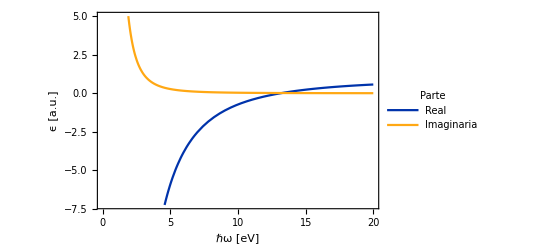

```mathematica
(*Definir la función para calcular la longitud de onda*)wavelength[eV_]:=1240/eV

(*Crear el gráfico*)
Plot[{Re[ϵDS[w,13.144,0.19716]],Im[ϵDS[w,13.144,0.19716]]},{w,0.1,20},Frame->True,PlotStyle->{RGBColor[0.,0.2,0.67],RGBColor[1.,0.66,0.08]},FrameLabel->{{"\!\(\*StyleBox[\"ϵ\",\nFontSize->18]\) [a.u.]",None},{"ℏω [eV]","λ [nm]"}},FrameStyle->Black,LabelStyle->{Directive[Bold,Black],FontFamily->"Helvetica",FontSize->14},PlotLegends->Placed[LineLegend[{"Real","Imaginaria"},LegendLabel->"Parte",LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],{0.75,0.3}],AxesOrigin->{0,0},FrameTicks->{Automatic,Automatic,Automatic,Table[{wavelength[x],x},{x,0.1,20,1}]}]
```

## Mie coefficients

```mathematica
hbarc=(299792458*10^9) * 6.582*10^(-16); (**[nm/s][eV s]**)
radi=1.; (**radio de la partícula en μm**)
Nmatriz = 1. ; (**Matriz:aire**)
sizepw[hw_]:=hw*radi*Nmatriz/hbarc (**Parametro de tamano**)
szw[hw_,r_]:=hw*r*Nmatriz/hbarc
```

```mathematica
an[n_,x_,m_]:= Module[{psix, dpsix,psimx, dpsimx,xi,dxi,an},
{psix,dpsix}={x*#,-n*#+x*SphericalBesselJ[n-1,x]}&@SphericalBesselJ[n,x];
{psimx,dpsimx}={m*x*#,-n*#+m*x*SphericalBesselJ[n-1,m*x]} &@SphericalBesselJ[n,m*x];
{xi,dxi}={psix,dpsix}+I*{#*x,-n*#+x*SphericalBesselY[n-1,x]}&@SphericalBesselY[n,x]; 
an=(m*psimx*dpsix-psix*dpsimx)/(m*psimx*dxi-xi*dpsimx);
an](***coeficiente an***)
bn[n_,x_,m_]:= Module[{psix, dpsix,psimx, dpsimx,xi,dxi,bn},
{psix,dpsix}={x*#,-n*#+x*SphericalBesselJ[n-1,x]}&@SphericalBesselJ[n,x];
{psimx,dpsimx}={m*x*#,-n*#+m*x*SphericalBesselJ[n-1,m*x]} &@SphericalBesselJ[n,m*x];
{xi,dxi}={psix,dpsix}+I*{#*x,-n*#+x*SphericalBesselY[n-1,x]}&@SphericalBesselY[n,x]; 
bn=(psimx*dpsix-m*psix*dpsimx)/(psimx*dxi-m*xi*dpsimx); 
bn](***coeficiente bn***)
anc[n_,x_,m_]:= Module[{psix, dpsix,psimx, dpsimx,xi,dxi,an},
{psix,dpsix}={x*#,-n*#+x*SphericalBesselJ[n-1,x]}&@SphericalBesselJ[n,x];
{psimx,dpsimx}={m*x*#,-n*#+m*x*SphericalBesselJ[n-1,m*x]} &@SphericalBesselJ[n,m*x];
{xi,dxi}={psix,dpsix}-I*{#*x,-n*#+x*SphericalBesselY[n-1,x]}&@SphericalBesselY[n,x]; 
an=(m*psimx*dpsix-psix*dpsimx)/(m*psimx*dxi-xi*dpsimx);
an](***coeficiente an conjundo***)
bnc[n_,x_,m_]:= Module[{psix, dpsix,psimx, dpsimx,xi,dxi,bn},
{psix,dpsix}={x*#,-n*#+x*SphericalBesselJ[n-1,x]}&@SphericalBesselJ[n,x];
{psimx,dpsimx}={m*x*#,-n*#+m*x*SphericalBesselJ[n-1,m*x]} &@SphericalBesselJ[n,m*x];
{xi,dxi}={psix,dpsix}-I*{#*x,-n*#+x*SphericalBesselY[n-1,x]}&@SphericalBesselY[n,x]; 
bn=(psimx*dpsix-m*psix*dpsimx)/(psimx*dxi-m*xi*dpsimx); bn
] (***coeficiente bn conjundo***)
Ce[n_,x_,m_]:=(2*Pi/(x/radi)^2)*Plus @@((2*#+1)*Re[an[#,x,m]+bn[#,x,m]]& /@ Range[n])
Cs[n_,x_,m_]:=(2*Pi/(x/radi)^2)*Plus @@((2*#+1)*(Abs[an[#,x,m]]^2 + Abs[bn[#,x,m]]^2) & /@ Range[n])
(***seccion transversal de extincion***)
Qe[n_,x_,m_]:=(2/(x^2))*Plus @@((2*#+1)*Re[an[#,x,m]+bn[#,x,m]]& /@ Range[n]) 
(***seccion transversal de extincion***)
Qs[n_,x_,m_]:=(2/(x^2))*Plus @@((2*#+1)*(Abs[an[#,x,m]]^2 + Abs[bn[#,x,m]]^2) & /@ Range[n]) 
Cer[n_,x_,m_,r_]:=(2*Pi/(x/r)^2)*Plus @@((2*#+1)*Re[an[#,x,m]+bn[#,x,m]]& /@ Range[n])
Csr[n_,x_,m_,r_]:=(2*Pi/(x/r)^2)*Plus @@((2*#+1)*(Abs[an[#,x,m]]^2 + Abs[bn[#,x,m]]^2) & /@ Range[n])
dan[n_,x_,m_]:=D[an[n,z,m],z]/.z->x (***derivada de coeficiente an***)
danc[n_,x_,m_]:=D[anc[n,z,m],z]/.z->x (***derivada coeficiente an conjundo***);
dbn[n_,x_,m_]:=D[bn[n,z,m],z]/.z->x (*** derivada de coeficiente bn***);
dbnc[n_,x_,m_]:=D[bnc[n,z,m],z]/.z->x;
dCepolos[x_,m_]:=Module[{dCeN,polos,dC},(***derivada del n esimo termino de Ce***)
polos =Range[wacombe]; (***criterio Wacombe***) 
  dCeN = Re@(((dan[polos, x, m] + dbn[polos, x, m])*x^2 ) - 2*x*(an[polos, x, m] + bn[polos, x, m]));
  dC = Plus @@ ((2.*# + 1 & /@ polos)*dCeN) ;
  dC *= ((2*Pi*radi^2)/x^4)]
dCe[x_,m_]:=Module[{dCeN,polos,dC},(***derivada del n esimo termino de Ce***)
polos=Range[Ceiling[x+4.*x^(1./3)+2.]];(***criterio Wacombe***)dCeN=Re@(((dan[polos,x,m]+dbn[polos,x,m])*x^2)-2*x*(an[polos,x,m]+bn[polos,x,m]));
dC=Plus@@((2.*#+1&/@polos)*dCeN);
dC*=((2*Pi*radi^2)/x^4)]
dCs[x_,m_]:=Module[{dCsN,polos,dC},(***derivada del n esimo termino de Ce***)
polos=Range[Ceiling[x+4.*x^(1./3)+2.]];(***criterio Wacombe***)dCsN=Re@(((anc[polos,x,m]*dan[polos,x,m]+an[polos,x,m]*danc[polos,x,m]+dbn[polos,x,m]*bnc[polos,x,m]+dbnc[polos,x,m]*bn[polos,x,m])*x^2)-2*x*(an[polos,x,m]*anc[polos,x,m]+bn[polos,x,m]*bnc[polos,x,m]));
dC=Plus@@((2.*#+1&/@polos)*dCsN);
dC*=((2*Pi*radi^2)/x^4)]
dCspolos[x_,m_]:=Module[{dCsN,polos,dC},(***derivada del n esimo termino de Ce***)
polos=Range[wacombe];(***criterio Wacombe***)dCsN=Re@(((anc[polos,x,m]*dan[polos,x,m]+an[polos,x,m]*danc[polos,x,m]+dbn[polos,x,m]*bnc[polos,x,m]+dbnc[polos,x,m]*bn[polos,x,m])*x^2)-2*x*(an[polos,x,m]*anc[polos,x,m]+bn[polos,x,m]*bnc[polos,x,m]));
dC=Plus@@((2.*#+1&/@polos)*dCsN);
dC*=((2*Pi*radi^2)/x^4)]
{evmax,evmin}=2*Pi*hbarc/# &@{350,750}(***rango visible***)
```

{3.54234,1.65309}

## Aluminium

```mathematica
ωp=13.142;
Γ=0.197;
radi=5;
Nmatriz=1;
sizepw[hw_]:=hw*radi*Nmatriz/hbarc (**Parametro de tamano**)
ωλ[λ_]:=hbarc* 2*π/(λ) 
evmin=4;
evmax=10;
wacombe=Max[Ceiling[(#*radi*Nmatriz/hbarc)+ 4.*(#*radi*Nmatriz/hbarc)^(1./3) + 2.] &@  {evmax,evmin} ];
mDS[w_,wp_,gamma_]:=nDS[w,wp,gamma]/Nmatriz
Qe[n_,x_,m_]:=(2/(x^2))*Plus @@((2*#+1)*Re[an[#,x,m]+bn[#,x,m]]& /@ Range[n]) (***seccion transversal de extincion***)
Qs[n_,x_,m_]:=(2/(x^2))*Plus @@((2*#+1)*(Abs[an[#,x,m]]^2 + Abs[bn[#,x,m]]^2) & /@ Range[n]) (***seccion transversal de esparcimiento***)
Qa[n_,x_,m_]:=Qe[n,x,m]-Qs[n,x,m]
```

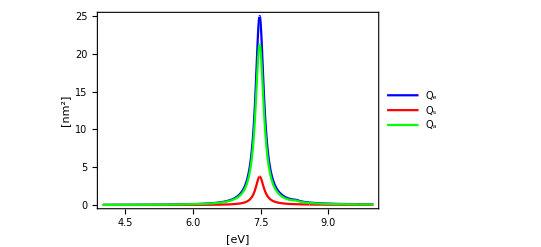

```mathematica
Plot[{Qe[wacombe,sizepw[w],mDS[w,ωp,Γ]],Qs[wacombe,sizepw[w],mDS[w,ωp,Γ]],Qa[wacombe,sizepw[w],mDS[w,ωp,Γ]]},{w,evmin,evmax},PlotRange->All,PlotStyle->{Blue, Red, Green},Frame->True,FrameLabel->{"[eV]","[nm^2]","Aluminio"},FrameStyle->Directive[Black,15, Bold],PlotLegends->Placed[{"Q_e","Q_s","Q_a"},{Left,Top}]]
```

## Gold

```mathematica
hbarc=(299792458*10^9) * 6.582*10^(-16); (**[nm/s][eV s]**)
radimax=1.; (**radio de la partícula en μm**)
Nmatriz = 1. ; (**Matriz:aire**)
sizepw[hw_,radio_]:=hw*radio*Nmatriz/hbarc
szepw[hw_]:=hw*radi*Nmatriz/hbarc
sizel[l_,radio_]:=2*Pi*radio*Nmatriz/l
ωλ[λ_]:=hbarc* 2*π/(λ) 
an[n_,x_,m_]:= Module[{psix, dpsix,psimx, dpsimx,xi,dxi,an},
{psix,dpsix}={x*#,-n*#+x*SphericalBesselJ[n-1,x]}&@SphericalBesselJ[n,x];
{psimx,dpsimx}={m*x*#,-n*#+m*x*SphericalBesselJ[n-1,m*x]} &@SphericalBesselJ[n,m*x];
{xi,dxi}={psix,dpsix}+I*{#*x,-n*#+x*SphericalBesselY[n-1,x]}&@SphericalBesselY[n,x]; 
an=(m*psimx*dpsix-psix*dpsimx)/(m*psimx*dxi-xi*dpsimx);
an](***coeficiente an***)
bn[n_,x_,m_]:= Module[{psix, dpsix,psimx, dpsimx,xi,dxi,bn},
{psix,dpsix}={x*#,-n*#+x*SphericalBesselJ[n-1,x]}&@SphericalBesselJ[n,x];
{psimx,dpsimx}={m*x*#,-n*#+m*x*SphericalBesselJ[n-1,m*x]} &@SphericalBesselJ[n,m*x];
{xi,dxi}={psix,dpsix}+I*{#*x,-n*#+x*SphericalBesselY[n-1,x]}&@SphericalBesselY[n,x]; 
bn=(psimx*dpsix-m*psix*dpsimx)/(psimx*dxi-m*xi*dpsimx); 
bn](***coeficiente bn***)
anc[n_,x_,m_]:= Module[{psix, dpsix,psimx, dpsimx,xi,dxi,an},
{psix,dpsix}={x*#,-n*#+x*SphericalBesselJ[n-1,x]}&@SphericalBesselJ[n,x];
{psimx,dpsimx}={m*x*#,-n*#+m*x*SphericalBesselJ[n-1,m*x]} &@SphericalBesselJ[n,m*x];
{xi,dxi}={psix,dpsix}-I*{#*x,-n*#+x*SphericalBesselY[n-1,x]}&@SphericalBesselY[n,x]; 
an=(m*psimx*dpsix-psix*dpsimx)/(m*psimx*dxi-xi*dpsimx);
an](***coeficiente an conjundo***)
bnc[n_,x_,m_]:= Module[{psix, dpsix,psimx, dpsimx,xi,dxi,bn},
{psix,dpsix}={x*#,-n*#+x*SphericalBesselJ[n-1,x]}&@SphericalBesselJ[n,x];
{psimx,dpsimx}={m*x*#,-n*#+m*x*SphericalBesselJ[n-1,m*x]} &@SphericalBesselJ[n,m*x];
{xi,dxi}={psix,dpsix}-I*{#*x,-n*#+x*SphericalBesselY[n-1,x]}&@SphericalBesselY[n,x]; 
bn=(psimx*dpsix-m*psix*dpsimx)/(psimx*dxi-m*xi*dpsimx); bn
] (***coeficiente bn conjundo***)
Ce[n_,x_,m_,radio_]:=(2*Pi/(x/radio)^2)*Plus @@((2*#+1)*Re[an[#,x,m]+bn[#,x,m]]& /@ Range[n]) (***seccion transversal de extincion***)
Cs[n_,x_,m_,radio_]:=(2*Pi/(x/radio)^2)*Plus @@((2*#+1)*(Abs[an[#,x,m]]^2 + Abs[bn[#,x,m]]^2) & /@ Range[n]) (***seccion transversal de extincion***)
Qe[n_,x_,m_]:=(2/(x^2))*Plus @@((2*#+1)*Re[an[#,x,m]+bn[#,x,m]]& /@ Range[n]) (***seccion transversal de extincion***)
Qs[n_,x_,m_]:=(2/(x^2))*Plus @@((2*#+1)*(Abs[an[#,x,m]]^2 + Abs[bn[#,x,m]]^2) & /@ Range[n]) (***seccion transversal de extincion***)
Qa[n_,x_,m_]:=Qe[n,x,m]-Qs[n,x,m]
dan[n_,x_,m_]:=D[an[n,z,m],z]/.z->x (***derivada de coeficiente an***)
danc[n_,x_,m_]:=D[anc[n,z,m],z]/.z->x (***derivada coeficiente an conjundo***);
dbn[n_,x_,m_]:=D[bn[n,z,m],z]/.z->x (*** derivada de coeficiente bn***);
dbnc[n_,x_,m_]:=D[bnc[n,z,m],z]/.z->x; (***derivada de coeficiente conjugado bn***)
dCepolos[x_,m_]:=Module[{dCeN,polos,dC},(***derivada del n esimo termino de Ce***)
polos =Range[wiscombe]; (***criterio wiscombe***) 
  dCeN = Re@(((dan[polos, x, m] + dbn[polos, x, m])*x^2 ) - 2*x*(an[polos, x, m] + bn[polos, x, m]));
  dC = Plus @@ ((2.*# + 1 & /@ polos)*dCeN) ;
  dC *= ((2*Pi*radi^2)/x^4)]
dCe[x_,m_]:=Module[{dCeN,polos,dC},(***derivada del n esimo termino de Ce***)
polos=Range[Ceiling[x+4.*x^(1./3)+2.]];(***criterio wiscombe***)dCeN=Re@(((dan[polos,x,m]+dbn[polos,x,m])*x^2)-2*x*(an[polos,x,m]+bn[polos,x,m]));
dC=Plus@@((2.*#+1&/@polos)*dCeN);
dC*=((2*Pi*radi^2)/x^4)]
dCs[x_,m_]:=Module[{dCsN,polos,dC},(***derivada del n esimo termino de Ce***)
polos=Range[Ceiling[x+4.*x^(1./3)+2.]];(***criterio wiscombe***)dCsN=Re@(((anc[polos,x,m]*dan[polos,x,m]+an[polos,x,m]*danc[polos,x,m]+dbn[polos,x,m]*bnc[polos,x,m]+dbnc[polos,x,m]*bn[polos,x,m])*x^2)-2*x*(an[polos,x,m]*anc[polos,x,m]+bn[polos,x,m]*bnc[polos,x,m]));
dC=Plus@@((2.*#+1&/@polos)*dCsN);
dC*=((2*Pi*radi^2)/x^4)]
dCspolos[x_,m_]:=Module[{dCsN,polos,dC},(***derivada del n esimo termino de Ce***)
polos=Range[wiscombe];(***criterio wiscombe***)dCsN=Re@(((anc[polos,x,m]*dan[polos,x,m]+an[polos,x,m]*danc[polos,x,m]+dbn[polos,x,m]*bnc[polos,x,m]+dbnc[polos,x,m]*bn[polos,x,m])*x^2)-2*x*(an[polos,x,m]*anc[polos,x,m]+bn[polos,x,m]*bnc[polos,x,m]));
dC=Plus@@((2.*#+1&/@polos)*dCsN);
dC*=((2*Pi*radi^2)/x^4)]
```

{2.43788,2.37575}

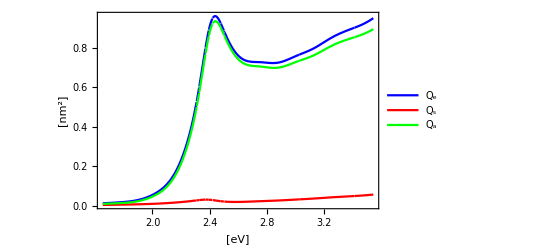

```mathematica
radimax=10;
{evmax,evmin}=(2*Pi*hbarc/#)&@{350,750};
wiscombemax=Max[Ceiling[(#1*radimax*Nmatriz/hbarc)+ 4.*(#1*radimax*Nmatriz/hbarc)^(1./3) + 2.] &@  {evmax,evmin} ];
radi=20;wacombe=Max[Ceiling[(#*radi*Nmatriz/hbarc)+ 4.*(#*radi*Nmatriz/hbarc)^(1./3) + 2.] &@  {evmax,evmin} ];
maxAu25nm={FindMaximum[{Ce[wacombe,sizepw[w,radi], rfindxAu[w],radi],2.4<=w<=2.47},{w,3.3}][[2]][[1]][[2]],
FindMaximum[{Cs[wacombe,sizepw[w,radi], rfindxAu[w],radi],2.29<=w<=2.47},{w,3.3}][[2]][[1]][[2]]}
au25plot=Plot[{Qe[wacombe,sizepw[w,radi],rfindxAu[w]],Qs[wacombe,sizepw[w,radi],rfindxAu[w]],Qa[wacombe,sizepw[w,radi],rfindxAu[w]]},{w,evmin,evmax},PlotRange->All,PlotStyle->{Blue, Red, Green},Frame->True,FrameLabel->{"[eV]","[nm^2]","Oro"},FrameStyle->Directive[Black,15, Bold],PlotLegends->Placed[{"Q_e","Q_s","Q_a"},{Left,Top}]]
```

## Plata (Ag)

{3.49436,3.48835}

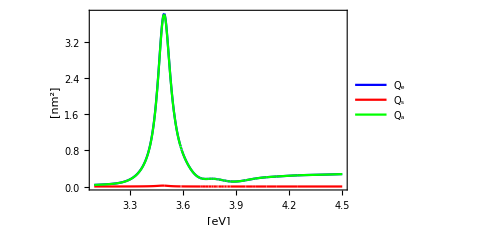

```mathematica
radi=5.0;
{evmax,evmin}=(2*Pi*hbarc/#)&@{350,750};
wiscombe=Max[Ceiling[(#*radi*Nmatriz/hbarc)+ 4.*(#*radi*Nmatriz/hbarc)^(1./3) + 2.] &@  {evmax,evmin} ];
(**Puntos máximos**)
maxAg25nm={FindMaximum[{Ce[wiscombe,sizepw[w,radi], rfindxAg[w],radi],3.3<=w<=3.5},{w,3.35}][[2]][[1]][[2]],
FindMaximum[{Cs[wiscombe,sizepw[w,radi], rfindxAg[w],radi],3.3<=w<=3.5},{w,3.35}][[2]][[1]][[2]]}
(**grafica**)
ag25plot=Plot[{Qe[wiscombe,sizepw[w,radi],rfindxAg[w]],Qs[wiscombe,sizepw[w,radi],rfindxAg[w]],Qa[wacombe,sizepw[w,radi],rfindxAg[w]]},{w,3.1,4.5},PlotRange->All,PlotStyle->{Blue, Red, Green},Frame->True,FrameLabel->{"[eV]","[nm^2]","Plata"},FrameStyle->Directive[Black,15, Bold],PlotLegends->Placed[{"Q_e","Q_s","Q_a"},{Left,Top}]]
```

## Silicio (Si)

{3.37106,3.4}

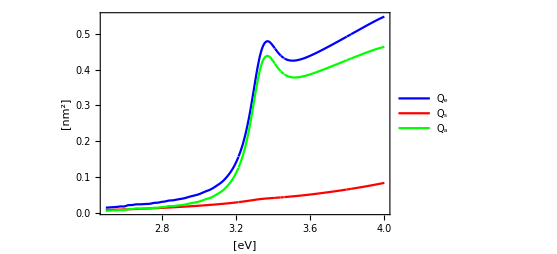

```mathematica
radi=20.0;
{evmax,evmin}=(2*Pi*hbarc/#)&@{350,750};
wiscombe=Max[Ceiling[(#*radi*Nmatriz/hbarc)+ 4.*(#*radi*Nmatriz/hbarc)^(1./3) + 2.] &@  {evmax,evmin} ];
(**maximos**)
maxSi25nm={FindMaximum[{Ce[wiscombe,sizepw[w,radi], rfindxSi[w],radi],3.2<=w<=3.4},{w,3.2}][[2]][[1]][[2]],
FindMaximum[{Cs[wiscombe,sizepw[w,radi], rfindxSi[w],radi],3.2<=w<=3.4},{w,3.2}][[2]][[1]][[2]]}
(**grafica**)
si25plot=Plot[{Qe[wiscombe,sizepw[w,radi],rfindxSi[w]],Qs[wiscombe,sizepw[w,radi],rfindxSi[w]],Qa[wacombe,sizepw[w,radi],rfindxSi[w]]},{w,2.5,4},PlotRange->All,PlotStyle->{Blue, Red, Green},Frame->True,FrameLabel->{"[eV]","[nm^2]","Silicio"},FrameStyle->Directive[Black,15, Bold],PlotLegends->Placed[{"Q_e","Q_s","Q_a"},{Left,Top}]]
```

## SiC

{5.4,6.5}

6.15663

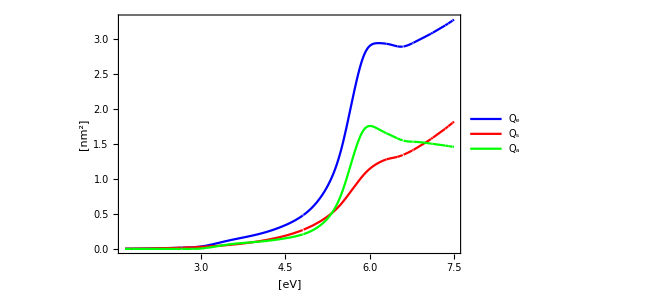

```mathematica
radi=25.0;
{evmax,evmin}=(2*Pi*hbarc/#)&@{350,750};
wiscombe=Max[Ceiling[(#*radi*Nmatriz/hbarc)+ 4.*(#*radi*Nmatriz/hbarc)^(1./3) + 2.] &@  {7.5,evmin} ];
{min1,max1}={5.4,6.5}
maxSiC25nm=FindMaximum[{Ce[wiscombe,sizepw[w,radi], rfindxSiC[w],radi],min1<=w<=max1},{w,3.2}][[2]][[1]][[2]]
(**grafica**)
sic25plot=Plot[{Qe[wiscombe,sizepw[w,radi],rfindxSiC[w]],Qs[wiscombe,sizepw[w,radi],rfindxSiC[w]],Qa[wacombe,sizepw[w,radi],rfindxSiC[w]]},{w,evmin,7.5},PlotRange->All,PlotStyle->{Blue, Red, Green},Frame->True,FrameLabel->{"[eV]","[nm^2]","Carburo de Silicio"},FrameStyle->Directive[Black,15, Bold],PlotLegends->Placed[{"Q_e","Q_s","Q_a"},{Left,Top}]]
```